# Computing and Plotting Wavelet Transformations

Orthogonal Wavelet Transformationspaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Transformations#154834215 | One-Sided Wavelet Transformspaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Transformations#214830535
Biorthogonal Wavelet Transformationspaclet:WaveletWare/tutorial/Computing and Plotting Wavelet Transformations#82101870 |

At the core of the WaveletWare package are several routines for computing different types of (bi)orthogonal wavelet transforms.  This tutorial describes how to use these functions and how to visualize results.  Some of the options for computing and visualizing transforms are not covered here but additional information can be found on particular function help pages.

This loads the package:

```mathematica
<<WaveletWare`
```

## Orthogonal Wavelet Transformations

(top)

The WaveletWare package includes two routines, HWTpaclet:WaveletWare/ref/HWT and WTpaclet:WaveletWare/ref/WT, for computing orthogonal wavelet transformations.  HWTpaclet:WaveletWare/ref/HWT computes the Haar wavelet transformation of the input (using the near-orthogonal filter {1/2,1/2}) and WTpaclet:WaveletWare/ref/WT computes the orthogonal wavelet transform resulting from the use of an orthogonal filter.  Built-in orthogonal filters include the Haar filter (Haarpaclet:WaveletWare/ref/Haar), Daubechies filters (Daubpaclet:WaveletWare/ref/Daub) and Coiflet filters (Coifpaclet:WaveletWare/ref/Coif).  User-defined orthogonal filters can also be used.  A third routine, WTFullpaclet:WaveletWare/ref/WTFull, generates several iterations of wavelet transformations.

HWT[data,opts] | Compute the Haar wavelet transformation
WT[data,filter,opts] | Compute an orthogonal wavelet transformation
WTFull[data,filter,opts] | Compute several iterations of wavelet transformations

Computing orthogonal wavelet transformations.

Haar[] | Haar filter
Daub[n,opts] | Daubechies filter of even length n
Coif[n,opts] | Coiflet filter of length 6n, n=1,2,3,4,5

Orthogonal filters.

The WaveletWare package contains a variety of routines that can be used for visualizing wavelet transforms.

WaveletVectorPlot[data,opts] | Plots the wavelet transform of 1-d data
FullWaveletVectorPlot[data,opts] | Plots all iterations of wavelet transforms of 1-d data
WaveletPlot[data,opts] | Plots the wavelet transform of a matrix or list of 3 matrices
FullWaveletPlot[data,opts] | Plots all iterations of a wavelet transform of input data
WaveletRegionPlot[data,region,opts] | Plots particular regions of the wavelet transform of input data

Routines to visualize wavelet transforms.

### One-Dimensional Haar Wavelet Transformations

(top of section)

We begin with one-dimensional transformations.  We start with the simple vector and apply HWTpaclet:WaveletWare/ref/HWT to this vector is equivalent to multiplying the vector by the matrix below.

```mathematica
v=Range[8]^2
W=WaveletMatrix[{1/2,1/2},{8,8}];
MatrixForm[W]
```

{1,4,9,16,25,36,49,64}

(1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2
-1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2)

```mathematica
HWT[v]
W.v //N
```

{2.5,12.5,30.5,56.5,1.5,3.5,5.5,7.5}

{2.5,12.5,30.5,56.5,1.5,3.5,5.5,7.5}

Setting the Orthogonalpaclet:WaveletWare/ref/Orthogonal option to True causes HWTpaclet:WaveletWare/ref/HWT to use the Haar filter.

```mathematica
v=Range[8]^2;
HWT[v,Orthogonal->True]
W=WaveletMatrix[Haar[],{8,8}];
MatrixForm[W]
W.v //N
```

{3.53553,17.6777,43.1335,79.9031,2.12132,4.94975,7.77817,10.6066}

(1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√2) | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 1/(√2)
-1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/(√2) | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 1/(√2))

{3.53553,17.6777,43.1335,79.9031,2.12132,4.94975,7.77817,10.6066}

Multiple iterations of the transformation can be computed (to the extent the data will allow).  Use the NumIterationspaclet:WaveletWare/ref/NumIterations option to control the number of iterations in the computation.  For the second iteration, HWTpaclet:WaveletWare/ref/HWT takes the first half  of the first iteration of the HWTpaclet:WaveletWare/ref/HWT and applies the HWTpaclet:WaveletWare/ref/HWT to it.

```mathematica
v=Range[8]^2;
HWT[v,NumIterations->2]
{low,high}=Partition[HWT[v],4]
Join[HWT[low],high]
```

{7.5,43.5,5.,13.,1.5,3.5,5.5,7.5}

{{2.5,12.5,30.5,56.5},{1.5,3.5,5.5,7.5}}

{7.5,43.5,5.,13.,1.5,3.5,5.5,7.5}

The routine WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot can be used to visualize one-dimensional transform output.

```mathematica
(* Donoho/Johnstone Doppler function *)
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1000;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

wt=HWT[v,NumIterations->3];
WaveletVectorPlot[wt,NumIterations->3,Ticks->{{125,250,500,1000},Range[-3/2,3/2]}]
```

-Graphics-

-Graphics-

WTFullpaclet:WaveletWare/ref/WTFull can be used to generate several iterations of an orthogonal wavelet transformation.

```mathematica
(* Donoho/Johnstone Doppler function *)
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1000;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

wt=WTFull[v,Haar[],NumIterations->3];
FullWaveletVectorPlot[wt]
```

-Graphics-

-Graphics-

The routine WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot can be used to plot particular regions of the wavelet transform.  The routine needs the input data and a list of regions to plot.  The items in the region list are lists themselves of length 2.  The first element is the iteration of the region and the second number is either 1 (lowpass) or 2 (highpass).   The only time the second number should be 1 is when the first number is the total number of iterations.

```mathematica
(* Donoho/Johnstone Doppler function *)
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1000;
v=g[Range[0,1-1/n,1/n]];

wt=WT[v,Daub[4],NumIterations->3];
(* Plot the third iteration *)
WaveletRegionPlot[wt,{{3,1},{3,2}},NumIterations->3]
(* Plot the highpass portion of the first iteration *)
WaveletRegionPlot[wt,{{1,2}},NumIterations->3]
```

-Graphics-

-Graphics-

### One-Dimensional Wavelet Transformations

(top of section)

In general, WTpaclet:WaveletWare/ref/WT can be used to compute orthogonal wavelet transforms with other filters.  The matrix computation is similar to that of the Haar wavelet transform.  

For example, computing the transform of an 8-vector using the Daubechies length 4 filter is the same as multiplying the vector by the following matrix:

```mathematica
(* Symbolic representation of the Daubechies filter of length 4 *)
h={1+Sqrt[3],3+Sqrt[3],3-Sqrt[3],1-Sqrt[3]}/4/Sqrt[2] // Simplify;
Daub[4]==h
W=WaveletMatrix[h,{8,8}];
MatrixForm[W]

v=Range[8]^2;
W.v //N
WT[v,Daub[4]]
```

True

(-(-1+√3)/(4 √2) | -(-3+√3)/(4 √2) | (3+√3)/(4 √2) | (1+√3)/(4 √2) | 0 | 0 | 0 | 0
0 | 0 | -(-1+√3)/(4 √2) | -(-3+√3)/(4 √2) | (3+√3)/(4 √2) | (1+√3)/(4 √2) | 0 | 0
0 | 0 | 0 | 0 | -(-1+√3)/(4 √2) | -(-3+√3)/(4 √2) | (3+√3)/(4 √2) | (1+√3)/(4 √2)
(3+√3)/(4 √2) | (1+√3)/(4 √2) | 0 | 0 | 0 | 0 | -(-1+√3)/(4 √2) | -(-3+√3)/(4 √2)
-(1+√3)/(4 √2) | (3+√3)/(4 √2) | (-3+√3)/(4 √2) | -(-1+√3)/(4 √2) | 0 | 0 | 0 | 0
0 | 0 | -(1+√3)/(4 √2) | (3+√3)/(4 √2) | (-3+√3)/(4 √2) | -(-1+√3)/(4 √2) | 0 | 0
0 | 0 | 0 | 0 | -(1+√3)/(4 √2) | (3+√3)/(4 √2) | (-3+√3)/(4 √2) | -(-1+√3)/(4 √2)
(-3+√3)/(4 √2) | -(-1+√3)/(4 √2) | 0 | 0 | 0 | 0 | -(1+√3)/(4 √2) | (3+√3)/(4 √2))

{16.0232,40.7212,76.7329,10.7725,-1.22474,-1.22474,-1.22474,29.1301}

{16.0232,40.7212,76.7329,10.7725,-1.22474,-1.22474,-1.22474,29.1301}

To the extent the data will allow, multiple iterations of the transform can be computed:

```mathematica
(* Donoho/Johnstone Doppler function *)
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1000;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

wt=WT[v,Coif[2],NumIterations->3];
WaveletVectorPlot[wt,NumIterations->3,Ticks->{{125,250,500,1000},Range[-3/2,3/2]}]
```

-Graphics-

-Graphics-

### Inverse One-Dimensional Wavelet Transformations

(top of section)

Each of HWTpaclet:WaveletWare/ref/HWT and WTpaclet:WaveletWare/ref/WT have an associated inverse function.  Since the wavelet matrices W (see above) are orthogonal, we have W^-1= W^T.

InverseHWT[data,opts] | Inverse Haar wavelet transformation
InverseWT[data,filter, opts] | Inverse orthogonal wavelet transformation

Inverse wavelet transformations.

```mathematica
v=Range[8]^2
wt=HWT[v]
iwt=InverseHWT[wt]
```

{1,4,9,16,25,36,49,64}

{2.5,12.5,30.5,56.5,1.5,3.5,5.5,7.5}

{1.,4.,9.,16.,25.,36.,49.,64.}

```mathematica
(* Donoho/Johnstone Doppler function *)
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1000;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v]

wt=WT[v,Daub[6],NumIterations->3];
iwt=InverseWT[wt,Daub[6],NumIterations->3];
Chop[v]==Chop[iwt]
ListPlot[iwt]
```

-Graphics-

True

-Graphics-

### Two-Dimensional Wavelet Transformations

(top of section)

For the wavelet transformation of an m x n matrix Apaclet:Global/ref/A, wavelet matrices W_m and W_n (see above) are formed, where even m, n represent the dimensions of the square matrices W_m and W_n, respectively, and then product W_mA W_n^T is computed.  Here is a simple example.

```mathematica
A=Table[i+j,{i,1,4},{j,1,6}];
MatrixForm[A]
{W4,W6}=Map[WaveletMatrix[{1/2,1/2},{#,#}]&,{4,6}];
Map[MatrixForm,{W4,W6}]
W4.A.Transpose[W6] // N // MatrixForm
HWT[A] // MatrixForm
```

(2 | 3 | 4 | 5 | 6 | 7
3 | 4 | 5 | 6 | 7 | 8
4 | 5 | 6 | 7 | 8 | 9
5 | 6 | 7 | 8 | 9 | 10)

{(1/2 | 1/2 | 0 | 0
0 | 0 | 1/2 | 1/2
-1/2 | 1/2 | 0 | 0
0 | 0 | -1/2 | 1/2),(1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2
-1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1/2)}

(3. | 5. | 7. | 0.5 | 0.5 | 0.5
5. | 7. | 9. | 0.5 | 0.5 | 0.5
0.5 | 0.5 | 0.5 | 0. | 0. | 0.
0.5 | 0.5 | 0.5 | 0. | 0. | 0.)

(3. | 5. | 7. | 0.5 | 0.5 | 0.5
5. | 7. | 9. | 0.5 | 0.5 | 0.5
0.5 | 0.5 | 0.5 | 0. | 0. | 0.
0.5 | 0.5 | 0.5 | 0. | 0. | 0.)

The WaveletWare package comes with a group of stock images that can be used in image processing applications.  The routines HWTpaclet:WaveletWare/ref/HWT and WTpaclet:WaveletWare/ref/WT can be applied to these images once they have been imported as matrices.  The output can be plotted using WaveletPlotpaclet:WaveletWare/ref/WaveletPlot, FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot or WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot.

```mathematica
f=PackageDirectory[DataType->Images]<>"car.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=WT[A,Coif[1]];
WaveletPlot[wt]
```

-Graphics-

-Graphics-

WaveletPlotpaclet:WaveletWare/ref/WaveletPlot can plot multiple iterations or even particular regions.

```mathematica
f=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=WT[A,Coif[1],NumIterations->3];
WaveletPlot[wt,NumIterations->3]
```

-Graphics-

-Graphics-

```mathematica
f=PackageDirectory[DataType->Images]<>"yucca.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=WT[A,Coif[1],NumIterations->3];
WaveletPlot[wt,NumIterations->3,Iteration->{{3,1,1},{3,2,2},{2,1,2},{1,2,2}}]
```

-Graphics-

-Graphics-

WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot can be used to plot particular regions of a transform.

```mathematica
f=PackageDirectory[DataType->Images]<>"chairs.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=WT[A,Coif[1],NumIterations->3];
WaveletRegionPlot[wt,{{3,1,1},{3,2,2},{2,1,2},{1,2,2}},NumIterations->3]
```

-Graphics-

-Graphics-

WTFullpaclet:WaveletWare/ref/WTFull can be used to compute several iterations of a wavelet transform and the results can be plotted using FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot:

```mathematica
f=PackageDirectory[DataType->Images]<>"road.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=WTFull[A,Daub[6],NumIterations->3];
FullWaveletPlot[wt]
```

-Graphics-

-Graphics-

### Inverse Wavelet Transforms of Matrices

(top of section)

Inverse wavelet transformations are computed using InverseHWTpaclet:WaveletWare/ref/InverseHWT or InverseWTpaclet:WaveletWare/ref/InverseWT.

```mathematica
f=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=WT[A,Coif[1]];
WaveletPlot[wt]

iwt=InverseWT[wt,Coif[1]];
ImagePlot[iwt]
Chop[iwt]==A
```

-Graphics-

-Graphics-

-Graphics-

True

### Wavelet Transformations and Color Images

(top of section)

The input for HWTpaclet:WaveletWare/ref/HWT and WTpaclet:WaveletWare/ref/WT can be lists of three matrices whose dimensions are the same.  Typically color images are converted to a different color space before they are processed by a wavelet transformation, but the capability to plot color output of wavelet transforms is built into the plotting routines.

```mathematica
f=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=HWT[A];
WaveletPlot[wt]
WaveletPlot[wt,PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

A more typical use of HWTpaclet:WaveletWare/ref/HWT and WTpaclet:WaveletWare/ref/WT for color images is image processing.  In these cases, the red, green, blue channels are converted to a different color space and then transforms are computed.  Here is an example using the YCbCr color space.

```mathematica
f=PackageDirectory[DataType->Images]<>"fish.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]
{y,cb,cr}=RGBToYCbCr[A,DisplayMode->True];
Map[ImagePlot,{y,cb,cr}]

wt=HWT[{y,cb,cr}];
WaveletPlot[wt]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Particular regions of wavelet transforms of color images can be plotted using WaveletPlotpaclet:WaveletWare/ref/WaveletPlot or WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot.  In this case, the option Iterationpaclet:WaveletWare/ref/Iteration becomes a list of lists each of the form {c,i,j,k} where c represents the channel (1,2,3), i is the iteration and (j,k) is the matrix block of that iteration to be displayed.  The value of c can also be All in which case the region (i,j,k) is plotted for all channels.

```mathematica
f=PackageDirectory[DataType->Images]<>"facade.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=HWT[A,NumIterations->3];
WaveletPlot[wt,NumIterations->3,Iteration->{{1,3,1,1},{3,1,2,2}}]
WaveletPlot[wt,NumIterations->3,Iteration->{{All,1,2,1}}]
WaveletPlot[wt,NumIterations->3,Iteration->{{All,1,2,1}},PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot can generate the equivalent output but the list of regions to be plotted is an argument rather than an option value.

```mathematica
f=PackageDirectory[DataType->Images]<>"waves.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=HWT[A,NumIterations->3];
WaveletRegionPlot[wt,{{1,3,1,1},{3,1,2,2}},NumIterations->3]
WaveletRegionPlot[wt,{{All,1,2,1}},NumIterations->3]
WaveletRegionPlot[wt,{{All,1,2,1}},NumIterations->3,PlotTogether->True]
```

-Graphics-

-Graphics-

{-Graphics-,-Graphics-}

-Graphics-

{-Graphics-}

WTFullpaclet:WaveletWare/ref/WTFull can be used for color images and the results can be plotted by FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot:

```mathematica
f=PackageDirectory[DataType->Images]<>"fish.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=WTFull[A,Daub[4],NumIterations->3];
FullWaveletPlot[wt]
FullWaveletPlot[wt,PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Particular regions can be plotted using FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot, but the value of Iterationpaclet:WaveletWare/ref/Iteration must be given as a list of lists, the length of which is the number of iterations plotted plus one.  The value All can serve as a list element.

```mathematica
f=PackageDirectory[DataType->Images]<>"facade.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=WTFull[A,Daub[4],NumIterations->2];
FullWaveletPlot[wt,Iteration->{All,{{1,1,1,2},{2,1,1,2},{3,1,1,2}},All}]
```

-Graphics-

-Graphics-

-Graphics-

### Inverse Wavelet Transformations of Color Images

(top of section)

InverseHWTpaclet:WaveletWare/ref/InverseHWT and InverseWTpaclet:WaveletWare/ref/InverseWT can be used to compute inverse transforms of color images or color space images.

```mathematica
f=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=HWT[A];
WaveletPlot[wt]
iwt=InverseHWT[wt];
ImagePlot[iwt]
Chop[iwt]==A
```

-Graphics-

-Graphics-

-Graphics-

True

```mathematica
f=PackageDirectory[DataType->Images]<>"waves.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

{h,s,i}=RGBToHSI[A];
wt=WT[{h,s,i},Daub[4],NumIterations->2];
WaveletPlot[wt,NumIterations->2]

iwt=Chop[InverseWT[wt,Daub[4],NumIterations->2]];

newA=HSIToRGB[iwt];
ImagePlot[newA]
```

-Graphics-

-Graphics-

-Graphics-

## Biorthogonal Wavelet Transformations

(top)

The WaveletWare package is equipped with two functions, BWTpaclet:WaveletWare/ref/BWT and LWTpaclet:WaveletWare/ref/LWT, that can be used to compute the biorthogonal wavelet transformation of a vector, matrix or a list of three matrices of equal dimensions.  A third function, WTFullpaclet:WaveletWare/ref/WTFull, can be used to compute many iterations of a biorthogonal wavelet transformation.  LWTpaclet:WaveletWare/ref/LWT is a routine that computes the biorthogonal wavelet transform using the LeGall 5/7 filter pair.  The computation is done using the lifting scheme and can be configured so that integer-valued data are transformed as integers.  BWTpaclet:WaveletWare/ref/BWT is used to compute a general biorthogonal wavelet transform.  Built-in biorthogonal filter pairs include spline filters (SplineFilterspaclet:WaveletWare/ref/SplineFilters), the Cohen-Daubechies-Feauveau 9/7 filter pair (CDF97paclet:WaveletWare/ref/CDF97) and the LeGall 5/7 filter pair (LeGallpaclet:WaveletWare/ref/LeGall).

The syntax for LWTpaclet:WaveletWare/ref/LWT and BWTpaclet:WaveletWare/ref/BWT is much the same as that of HWTpaclet:WaveletWare/ref/HWT and WTpaclet:WaveletWare/ref/WT, respectively, except that there are options available to map integers to integers (LWTpaclet:WaveletWare/ref/LWT) and exploit the symmetric nature of the built-in biorthogonal filter pairs (see the Boundarypaclet:WaveletWare/ref/Boundary option).

LWT[data,opts] | Compute the LeGall biorthogonal wavelet transformation
BWT[data,filter,opts] | Compute a biorthogonal wavelet transformation
WTFull[data,filter,opts] | Compute several iterations of wavelet transformations

Computing biorthogonal wavelet transformations.

LeGall[] | LeGall 5/7 biorthogonal filter pair
CDF97[] | Cohen-Daubechies-Feauveau biorthogonal filter pair
SplineFilters[n,m] | Spline filter pair, m,n integers of the same parity

Built-in biorthogonal filter pairs.

### One-Dimensional Biorthogonal Wavelet Transformations

(top of section)

Unlike orthogonal wavelet transformations, biorthogonal transformations use a pair of filters to generate the transformation matrix.  The cell below shows the (5,3) spline filter pair.  Starting indices of these filters are -2 and -1, respectively.

```mathematica
SplineFilters[2,2]
```

{{-1/(4 √2),1/(2 √2),3/(2 √2),1/(2 √2),-1/(4 √2)},{1/(2 √2),1/(√2),1/(2 √2)}}

The matrix for performing the transformation is shown below in the 8x8 case.  Note the top half of the matrix is constructed from cyclic shifts of the length 3 filter (with the 0 subscript term in the (1,1) position) and the bottom half constructed from shifts of the first filter with alternating signs.  In particular, if the first filter has values h_k, k=-2,...,2, then the filter on the bottom is defined by g_k= (-1)^kh_(1-k), k=-1,...,3.  Thus, g_0is located in the (5,1) position and other rows are obtained by cyclic shifts.

```mathematica
W=WaveletMatrix[SplineFilters[2,2],{8,8}];
MatrixForm[W]
```

(1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 1/(2 √2)
0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2)
1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 1/(4 √2)
0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0
0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2)
1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2))

Applying this matrix to a vector is equivalent to applying BWTpaclet:WaveletWare/ref/BWT to the vector.

```mathematica
v=Range[8]^2;
W.v // N
BWT[v,SplineFilters[2,2]] // Chop
```

{24.7487,13.435,36.0624,70.0036,13.435,2.12132,2.12132,-43.1335}

{24.7487,13.435,36.0624,70.0036,13.435,2.12132,2.12132,-43.1335}

### The Inverse One-Dimensional Biorthogonal Wavelet Transformation

(top of section)

For orthogonal transformations, we used a single filter to generate an orthogonal matrix Wpaclet:Global/ref/W and in this case, W^-1= W^T.  A matrix Wpaclet:Global/ref/W, such as the one generated from the (5,3) spline filter pair is not orthogonal, but its inverse has an amazing property.

```mathematica
W=WaveletMatrix[SplineFilters[2,2],{8,8}];
Print["W = ",MatrixForm[W],"."];
Print["The transpose of the inverse of W is ",MatrixForm[Transpose[Inverse[W]]]];
```

W = (1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 1/(2 √2)
0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2)
1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 1/(4 √2)
0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0
0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2)
1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2)).

The transpose of the inverse of W is (3/(2 √2) | 1/(2 √2) | -1/(4 √2) | 0 | 0 | 0 | -1/(4 √2) | 1/(2 √2)
-1/(4 √2) | 1/(2 √2) | 3/(2 √2) | 1/(2 √2) | -1/(4 √2) | 0 | 0 | 0
0 | 0 | -1/(4 √2) | 1/(2 √2) | 3/(2 √2) | 1/(2 √2) | -1/(4 √2) | 0
-1/(4 √2) | 0 | 0 | 0 | -1/(4 √2) | 1/(2 √2) | 3/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(2 √2) | -1/(√2) | 1/(2 √2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 √2) | -1/(√2) | 1/(2 √2) | 0
1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 1/(2 √2) | -1/(√2))

Note that the transpose of the inverse of Wpaclet:Global/ref/W is simply the matrix we would have obtained had we generated a wavelet matrix from the (2,2) spline filter pair with the order of the filters reversed!

```mathematica
WaveletMatrix[Reverse[SplineFilters[2,2]],{8,8}] // MatrixForm
```

(3/(2 √2) | 1/(2 √2) | -1/(4 √2) | 0 | 0 | 0 | -1/(4 √2) | 1/(2 √2)
-1/(4 √2) | 1/(2 √2) | 3/(2 √2) | 1/(2 √2) | -1/(4 √2) | 0 | 0 | 0
0 | 0 | -1/(4 √2) | 1/(2 √2) | 3/(2 √2) | 1/(2 √2) | -1/(4 √2) | 0
-1/(4 √2) | 0 | 0 | 0 | -1/(4 √2) | 1/(2 √2) | 3/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(2 √2) | -1/(√2) | 1/(2 √2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 √2) | -1/(√2) | 1/(2 √2) | 0
1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 1/(2 √2) | -1/(√2))

If we set Wpaclet:Global/ref/W to be the  biorthogonal wavelet matrix generated from the filter pair (h,h̃), then the inverse of Wpaclet:Global/ref/W is simply the transpose of the wavelet matrix W̃ generated from the filter pair (h̃,h).

```mathematica
v=Range[8]^2;
wt=BWT[v,SplineFilters[2,2]]
Wtilde=Transpose[WaveletMatrix[Reverse[SplineFilters[2,2]],{8,8}]];
MatrixForm[Wtilde]
Wtilde.wt
InverseBWT[wt,SplineFilters[2,2]]
```

{24.7487,13.435,36.0624,70.0036,13.435,2.12132,2.12132,-43.1335}

(3/(2 √2) | -1/(4 √2) | 0 | -1/(4 √2) | 1/(2 √2) | 0 | 0 | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 0 | 0 | -1/(√2) | 0 | 0 | 0
-1/(4 √2) | 3/(2 √2) | -1/(4 √2) | 0 | 1/(2 √2) | 1/(2 √2) | 0 | 0
0 | 1/(2 √2) | 1/(2 √2) | 0 | 0 | -1/(√2) | 0 | 0
0 | -1/(4 √2) | 3/(2 √2) | -1/(4 √2) | 0 | 1/(2 √2) | 1/(2 √2) | 0
0 | 0 | 1/(2 √2) | 1/(2 √2) | 0 | 0 | -1/(√2) | 0
-1/(4 √2) | 0 | -1/(4 √2) | 3/(2 √2) | 0 | 0 | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | 0 | 0 | 1/(2 √2) | 0 | 0 | 0 | -1/(√2))

{1.,4.,9.,16.,25.,36.,49.,64.}

{1.,4.,9.,16.,25.,36.,49.,64.}

### Exploiting the Symmetry of Biorthogonal Filters

(top of section)

It is possible to configure BWTpaclet:WaveletWare/ref/BWT via the Boundarypaclet:WaveletWare/ref/Boundary option to take advantage of the symmetric nature of built-in biorthogonal spline filter pairs (or user-created symmetric pairs).  The output of a biorthogonal wavelet transform is plotted below.

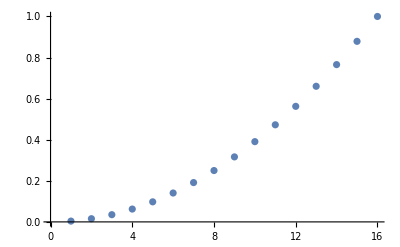

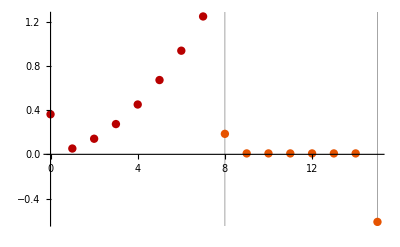

```mathematica
v=Range[16]^2/256;
ListPlot[v]
wt=BWT[v,SplineFilters[2,2]];
WaveletVectorPlot[wt,ImageSize->400,PointSize->.015]
```

Note that the first term from the lowpass portion of the transform and the first and last terms of the highpass portion of the transform show the effects of the "wrap around" rows of the inherent biorthogonal wavelet matrix.  Below is the output with Boundarypaclet:WaveletWare/ref/Boundary set to True.

-Graphics-

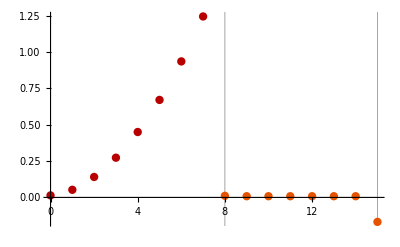

```mathematica
v=Range[16]^2/256;
ListPlot[v]
wt=BWT[v,SplineFilters[2,2],Boundary->True];
WaveletVectorPlot[wt,ImageSize->400,PointSize->.015]
```

When Boundarypaclet:WaveletWare/ref/Boundary is set to True, BWTpaclet:WaveletWare/ref/BWT, for biorthogonal filters each with odd length, creates the following periodic vector from the input.

```mathematica
v=Range[8]^2
vperiodic=Join[v,Reverse[Take[v,{2,7}]]]
```

{1,4,9,16,25,36,49,64}

{1,4,9,16,25,36,49,64,49,36,25,16,9,4}

Next, a wavelet matrix of size 14x14 is created and applied to the new vector.

```mathematica
W=WaveletMatrix[SplineFilters[2,2],{14,14}];
MatrixForm[W]
W.vperiodic // N
```

(1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √2)
0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √2) | 1/(√2) | 1/(2 √2)
1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(4 √2)
0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2) | 1/(2 √2) | 1/(4 √2)
1/(2 √2) | 1/(4 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(4 √2) | 1/(2 √2) | -3/(2 √2))

{3.53553,13.435,36.0624,70.0036,70.0036,36.0624,13.435,2.82843,2.12132,2.12132,-20.5061,2.12132,2.12132,2.82843}

Note that the first element of the output is computed using v_1,v_2, v_2 (now at the end of our periodic vector) rather than v_1,v_2, v_8 were we to have used the 8x8 wavelet matrix.  Similar observations hold for the wrap around rows in the highpass portion of the transform.  

Note also the symmetric nature of the lowpass and highpass portions of the transform.  Indeed we discard the last three elements of the lowpass and highpass portions of the output to arrive at our modified transform.  The result can be seen using BWTpaclet:WaveletWare/ref/BWT with Boundarypaclet:WaveletWare/ref/Boundary set to True.

```mathematica
BWT[v,SplineFilters[2,2],Boundary->True]
```

{3.53553,13.435,36.0624,70.0036,2.82843,2.12132,2.12132,-20.5061}

The procedure for inverting "symmetric" transforms is straightforward.  The lowpass and highpass portions of the output are padded as above, the inverse transform is computed and then the extraneous elements of the output are dropped.

```mathematica
v=Range[8]^2;
wt=BWT[v,SplineFilters[2,2],Boundary->True]
{lp,hp}=Partition[wt,4];
newlp=Join[lp,Reverse[Rest[lp]]];
newhp=Join[hp,Reverse[Most[hp]]];
newwt=Join[newlp,newhp]
Wtilde=Transpose[WaveletMatrix[Reverse[SplineFilters[2,2]],{14,14}]];
vperiodic=Wtilde.newwt
Take[vperiodic,8]
```

{3.53553,13.435,36.0624,70.0036,2.82843,2.12132,2.12132,-20.5061}

{3.53553,13.435,36.0624,70.0036,70.0036,36.0624,13.435,2.82843,2.12132,2.12132,-20.5061,2.12132,2.12132,2.82843}

{1.,4.,9.,16.,25.,36.,49.,64.,49.,36.,25.,16.,9.,4.}

{1.,4.,9.,16.,25.,36.,49.,64.}

```mathematica
InverseBWT[wt,SplineFilters[2,2],Boundary->True]
```

{1.,4.,9.,16.,25.,36.,49.,64.}

When Boundarypaclet:WaveletWare/ref/Boundary is set to True for even-length filter pairs, the periodic vector is formed by adjoining the original vector with a reverse of itself and proceeding in a method similar to that described above.

### Two-Dimensional Biorthogonal Wavelet Transformations

(top of section)

The biorthogonal filter pair (h,h̃) gives rise to wavelet matrices W and W̃ described earlier in this section.  The construction guarantees that W^-1= (W̃)^T.  As in the case of orthogonal transforms of matrices where the input matrix A was pre- and post-multiplied by W and W^T(W^-1), respectively, the biorthogonal transform of matrix A is obtained from the product WA(W̃)^T.

Plotting biorthogonal wavelet transforms can be done with the visualization routines described above.

```mathematica
f=PackageDirectory[DataType->Images]<>"road.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=BWT[A,SplineFilters[3,1]];
WaveletPlot[wt]
```

-Graphics-

-Graphics-

```mathematica
f=PackageDirectory[DataType->Images]<>"chairs.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=BWT[A,SplineFilters[3,1],NumIterations->3,Boundary->True];
WaveletPlot[wt,NumIterations->3]
iwt=InverseBWT[wt,SplineFilters[3,1],NumIterations->3,Boundary->True];
ImagePlot[iwt]
A==Chop[iwt]
```

-Graphics-

-Graphics-

-Graphics-

True

### Biorthogonal Wavelet Transformations and Color Images

(top of section)

The computation and visualization of biorthogonal wavelet transformations involving color images is similar to the procedure described above for computing and plotting wavelet transformations of color images.

```mathematica
f=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=BWT[A,CDF97[],NumIterations->2];
WaveletPlot[wt,NumIterations->2]
WaveletPlot[wt,NumIterations->2,PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
f=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=BWT[A,CDF97[],NumIterations->2];
WaveletPlot[wt,NumIterations->2]

iwt=InverseBWT[wt,CDF97[],NumIterations->2];
ImagePlot[iwt]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### LeGall Biorthogonal Wavelet Transformation

(top of section)

The LeGall 5/3 biorthogonal filter pair is used for lossless compression in the JPEG2000 Image Compression Standard.  It can be computed using the BWTpaclet:WaveletWare/ref/BWT module and an adjusted LeGallpaclet:WaveletWare/ref/LeGall filter pair:

```mathematica
v=Range[8]^2;
{h,ht}=Reverse[LeGall[]];
BWT[v,{-h,ht},Boundary->True]
LWT[v]
```

{0.5,8.5,24.5,52.5,-1.,-1.,-1.,15.}

{0.5,8.5,24.5,52.5,-1.,-1.,-1.,15.}

The reason the LeGall transform is used in lossless compression is that the computation of the transform is done via the lifting method and as a result, rounding can be incorporated to produce an invertible transformation that maps integers to integers.  

The lifting algorithm for the LeGall filter is as follows:  Partition input vector v (of even length Npaclet:ref/N) into even e and odd o vectors.  Then the highpass portion d and lowpass portion s are computed element-wise by:

d_k= e_k- 1/2(o_k+ o_(k+1)) and then s_k= o_k +  1/4(d_k+ d_(k-1)).

Here, k=1,...,Npaclet:ref/N/2 with o_(N/2+1) = o_(N/2) and d_0 = d_1.  The formulas for recovering the odd and even vectors are easily obtained from the formulas for d_kand s_k.

To map integers to integers, replace the formulas above by 

d_k= e_k- Floor[1/2(o_k+ o_(k+1))] and then s_k= Floor[o_k +  1/4(d_k+ d_(k-1)) + 1/2].

To implement the integer-to-integer version of the LeGall transform, set IntegerMappaclet:WaveletWare/ref/IntegerMap to True in LWTpaclet:WaveletWare/ref/LWT.

```mathematica
v=Range[8]^2;
LWT[v]
LWT[v,IntegerMap->True]
```

{0.5,8.5,24.5,52.5,-1.,-1.,-1.,15.}

{1,9,25,53,-1,-1,-1,15}

The integer-to-integer version of the LeGall wavelet transform is invertible:

```mathematica
v=Range[8]^2
wt=LWT[v,IntegerMap->True]
iwt=InverseLWT[wt,IntegerMap->True]
```

{1,4,9,16,25,36,49,64}

{1,9,25,53,-1,-1,-1,15}

{1,4,9,16,25,36,49,64}

## One-Sided Wavelet Transforms

(top)

For primarily pedagogical reasons it is desirable to compute the "left" or "right" (biorthogonal) wavelet transform of a matrix or list of three matrices.  In the case of the former for a matrix, left-transform routines compute WA, where W is a wavelet matrix and A is the input matrix.  In the case of the latter for a matrix, the right-transform routines compute AW^Tif W is generated from an orthogonal filter and A(W̃)^T, if W, W̃ are generated from a biorthogonal pair.  All transform routines above have analogous left- and right-transforms.

LeftBWT[data,filter,opts] | Compute the left biorthogonal wavelet transform
LeftHWT[data,opts] | Compute the left Haar wavelet transform
LeftLWT[data,opts] | Compute the left LeGall wavelet transform
LeftWT[data,filter,opts] | Compute the left orthogonal wavelet transform
RightBWT[data,filter,opts] | Compute the right biorthogonal wavelet transform
RighHWT[data,opts] | Compute the right Haar wavelet transform
RightLWT[data,opts] | Compute the right LeGall wavelet transform
RightWT[data,filter,opts] | Compute the right orthogonal wavelet transform

One-sided wavelet transforms.

The WaveletPlotpaclet:WaveletWare/ref/WaveletPlot routine can be used to plot left- and right-transforms.  The option PlotTypepaclet:WaveletWare/ref/PlotType can be set to Left or Right to plot the appropriate transform.

### One-Sided Wavelet Transforms of Matrices

(top of section)

Compute and plot the left- and right-transforms of a matrix.

```mathematica
f=PackageDirectory[DataType->Images]<>"road.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

lwt=LeftHWT[A];
WaveletPlot[lwt,PlotType->Left]

rwt=RightHWT[A];
WaveletPlot[rwt,PlotType->Right]
```

-Graphics-

-Graphics-

-Graphics-

For routines like LeftWTpaclet:WaveletWare/ref/LeftWT, LeftBWTpaclet:WaveletWare/ref/LeftBWT, RightWTpaclet:WaveletWare/ref/RightWT, RightBWTpaclet:WaveletWare/ref/RightBWT, a filter (pair) must be specified.

```mathematica
f=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

lwt=LeftWT[A,Daub[4]];
WaveletPlot[lwt,PlotType->Left]

rwt=RightBWT[A,SplineFilters[2,2]];
WaveletPlot[rwt,PlotType->Right]
```

-Graphics-

-Graphics-

-Graphics-

### One-Sided Wavelet Transforms and Color

(top of section)

All of the one-sided wavelet transform routines accept as input a list of three matrices whose dimensions are equal.  This facilitates plotting color transforms or transforms in different color spaces.

```mathematica
f=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
MapThread[ImagePlot[#1,ChannelColor->#2]&,{A,{Red,Green,Blue}}]

wt=LeftLWT[A];
WaveletPlot[wt,PlotType->Left]
WaveletPlot[wt,PlotType->Left,ChannelColor->{Red,Green,Blue}]
WaveletPlot[wt,PlotType->Left,PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

In the cell below, a color image is converted to YCbCr space and then the right-transform of each channel is computed and plotted.

```mathematica
f=PackageDirectory[DataType->Images]<>"fish.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]
{y,cb,cr}=RGBToYCbCr[A];
Map[ImagePlot[#,Scaling->True]&,{y,cb,cr}]

rwt=RightHWT[{y,cb,cr}];
WaveletPlot[rwt,PlotType->Right]
```

-Graphics-

-Graphics-

-Graphics-

Related Tutorials

Computing and Plotting Wavelet Packet Transformations

Naive Image Compression and Edge Detection